ΜΣΜ 61  
5η Γραπτή Εργασία
Λυμπερίδης Σταύρος   Α.Μ.: 91076

Ασκηση 1

α)

Όπως τις σημειώσεις MΗΟΜΟΓΕΝΗΣΕΞΘΕΡΜ.

β)

ι)

```mathematica
ClearAll["Global`*"]

L:=1
Subscript[T, 1]:=1
Subscript[T, 2]:=2
f[x_]:=0
S[x_]:=Subscript[T, 1]+((Subscript[T, 2]-Subscript[T, 1])x)/L
Print["Για t->∞ η λύση προσεγγίζει ασυμπτωτικά την συνάρτηση: ",S[x]]
Print["Παρακάτω παρατηρούμε ότι η NDsolve μας προειδοποιεί πως δεν ικανοποιούνται οι αρχικές συνθήκες: "]
pde=  D[U[x,t],t]== D[U[x,t],{x,2}];
bc1=U[0,t]==Subscript[T, 1];
bc2=U[L,t]==Subscript[T, 2];
ic=U[x,0]==f[x];
nsol=NDSolve[{pde,bc1,bc2,ic},{U},{x,0,L},{t,0,10},MaxStepSize->10000,MaxSteps->10000];
z=nsol[[1,1,2]];

Plot3D[ z[x,t],{x,0,L},{t,0,10},AxesLabel->{x,t,"z"},PlotRange->All,ColorFunction->"TemperatureMap",LabelStyle->Directive[Blue,FontWeight->Bold,FontSize->12,FontFamily->"Arial"],ImageSize->500]

Manipulate[Plot[z[x,t], {x,0,L},PlotRange->All,AxesLabel->{x,"z"},PlotStyle-> Thick   ,ImageSize->500 ,PlotLabel->{"t=",t}],{t,0,10}]
```

Για t->∞ η λύση προσεγγίζει ασυμπτωτικά την συνάρτηση: 1+x

Παρακάτω παρατηρούμε ότι η NDsolve μας προειδοποιεί πως δεν ικανοποιούνται οι αρχικές συνθήκες:

NDSolve::ibcinc: Warning: boundary and initial conditions are inconsistent.

-Graphics3D-

ιι)

```mathematica
ClearAll["Global`*"]

L:=1
Subscript[T, 1]:=1
Subscript[T, 2]:=2
f[x_]:=Subscript[T, 1](1-x^2/L^2)+(Subscript[T, 2] x)/L
S[x_]:=Subscript[T, 1]+((Subscript[T, 2]-Subscript[T, 1])x)/L
Print["Για t->∞ η λύση προσεγγίζει ασυμπτωτικά την συνάρτηση: ",S[x]]
pde=  D[U[x,t],t]== D[U[x,t],{x,2}];
bc1=U[0,t]==Subscript[T, 1];
bc2=U[L,t]==Subscript[T, 2];
ic=U[x,0]==f[x];
nsol=NDSolve[{pde,bc1,bc2,ic},{U},{x,0,L},{t,0,10},MaxStepSize->10000,MaxSteps->10000];
z=nsol[[1,1,2]];

Plot3D[ z[x,t],{x,0,L},{t,0,0.5},AxesLabel->{x,t,"z"},PlotRange->All,ColorFunction->"TemperatureMap",LabelStyle->Directive[Blue,FontWeight->Bold,FontSize->12,FontFamily->"Arial"],ImageSize->500]

Manipulate[Plot[z[x,t], {x,0,L},PlotRange->All,AxesLabel->{x,"z"},PlotStyle-> Thick   ,ImageSize->500 ,PlotLabel->{"t=",t}],{t,0,1}]
```

Για t->∞ η λύση προσεγγίζει ασυμπτωτικά την συνάρτηση: 1+x

-Graphics3D-

γ)

```mathematica
L:=1
Subscript[T, 1]:=1
Subscript[T, 2]:=2
f[x_]=Subscript[T, 1](1-x^2/L^2)+(Subscript[T, 2] x)/L;
S[x_]=Subscript[T, 1]+((Subscript[T, 2]-Subscript[T, 1])x)/L;
Solution[x_,t_,N_]=S[x]+Sum[c[n]*Sin[(n*Pi*x)/L]*E^(-(n^2 Pi^2 t)/L^2),{n,1,N}];
c[n_]=2/L∫_0^L (f[x]-S[x])*Sin[(n*Pi*x)/L]ⅆx;

Sol[x_,t_]=Solution[x,t,20];

Plot3D[Sol[x,t] ,{x,0,L},{t,0,2},AxesLabel->{x,t,"z"},PlotRange->All,ColorFunction->"TemperatureMap",LabelStyle->Directive[Blue,FontWeight->Bold,FontSize->12,FontFamily->"Arial"],ImageSize->500]
```

-Graphics3D-

δ)

```mathematica
(* Τα σημεία ανήκουν στο ορθογώνιο [0,1]x[0,4] *)
data1=Table[  {1/7i,4/7j }     ,{i,0,7},{j,0,7}]   ;
data2=Table[  z[1/7i,4/7j ]     ,{i,0,7},{j,0,7}]    ;
data3=Table[  N[Sol[1/7i,4/7j ],6]   ,{i,0,7},{j,0,7}]   ;
data4=Table[Abs[z[1/7i,4/7j ]-Sol[1/7i,4/7j ]] ,{i,0,7},{j,0,7}] ;
TableForm[{data1,data2,data3 ,data4}, TableAlignments->Center,TableSpacing->{4,1},TableHeadings->{{"κ:03ccμβος", "προσ. τιμ:03ae" ,"ακριβ:03aeς τιμ:03ae ","σφ:03acλμα"},Automatic}]
```

| 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8
κόμβος | 0 | 0
0 | 4/7
0 | 8/7
0 | 12/7
0 | 16/7
0 | 20/7
0 | 24/7
0 | 4 | 1/7 | 0
1/7 | 4/7
1/7 | 8/7
1/7 | 12/7
1/7 | 16/7
1/7 | 20/7
1/7 | 24/7
1/7 | 4 | 2/7 | 0
2/7 | 4/7
2/7 | 8/7
2/7 | 12/7
2/7 | 16/7
2/7 | 20/7
2/7 | 24/7
2/7 | 4 | 3/7 | 0
3/7 | 4/7
3/7 | 8/7
3/7 | 12/7
3/7 | 16/7
3/7 | 20/7
3/7 | 24/7
3/7 | 4 | 4/7 | 0
4/7 | 4/7
4/7 | 8/7
4/7 | 12/7
4/7 | 16/7
4/7 | 20/7
4/7 | 24/7
4/7 | 4 | 5/7 | 0
5/7 | 4/7
5/7 | 8/7
5/7 | 12/7
5/7 | 16/7
5/7 | 20/7
5/7 | 24/7
5/7 | 4 | 6/7 | 0
6/7 | 4/7
6/7 | 8/7
6/7 | 12/7
6/7 | 16/7
6/7 | 20/7
6/7 | 24/7
6/7 | 4 | 1 | 0
1 | 4/7
1 | 8/7
1 | 12/7
1 | 16/7
1 | 20/7
1 | 24/7
1 | 4
προσ. τιμή | 1.
1.
1.
1.
1.
1.
1.
1. | 1.26531
1.14326
1.14286
1.14286
1.14286
1.14286
1.14286
1.14286 | 1.4898
1.28644
1.28571
1.28571
1.28571
1.28571
1.28571
1.28571 | 1.67347
1.42948
1.42857
1.42857
1.42857
1.42857
1.42857
1.42857 | 1.81633
1.57233
1.57143
1.57143
1.57143
1.57143
1.57143
1.57143 | 1.91837
1.71501
1.71429
1.71429
1.71429
1.71429
1.71429
1.71429 | 1.97959
1.85755
1.85714
1.85714
1.85714
1.85714
1.85714
1.85714 | 2.
2.
2.
2.
2.
2.
2.
2.
ακριβής τιμή  | 1.
1.
1.
1.
1.
1.
1.
1. | 1.26533
1.14325
1.14286
1.14286
1.14286
1.14286
1.14286
1.14286 | 1.48979
1.28643
1.28572
1.28571
1.28571
1.28571
1.28571
1.28571 | 1.67347
1.42947
1.42857
1.42857
1.42857
1.42857
1.42857
1.42857 | 1.81633
1.57232
1.57143
1.57143
1.57143
1.57143
1.57143
1.57143 | 1.91836
1.715
1.71429
1.71429
1.71429
1.71429
1.71429
1.71429 | 1.97962
1.85754
1.85714
1.85714
1.85714
1.85714
1.85714
1.85714 | 2.
2.
2.
2.
2.
2.
2.
2.
σφάλμα | 0.
0.
0.
0.
0.
0.
0.
0. | 0.0000256746
4.91071×10^-6
1.23293×10^-6
6.84729×10^-9
7.43471×10^-9
1.29594×10^-9
5.49399×10^-10
1.53639×10^-11 | 0.0000106525
8.6727×10^-6
2.22171×10^-6
1.23376×10^-8
1.33969×10^-8
2.33521×10^-9
9.89986×10^-10
2.76847×10^-11 | 3.09255×10^-6
0.0000108925
2.77041×10^-6
1.53846×10^-8
1.67058×10^-8
2.91197×10^-9
1.23448×10^-9
3.45246×10^-11 | 3.09255×10^-6
0.0000108925
2.77041×10^-6
1.53845×10^-8
1.67057×10^-8
2.91199×10^-9
1.23447×10^-9
3.45266×10^-11 | 0.0000106525
8.6727×10^-6
2.22171×10^-6
1.23376×10^-8
1.33969×10^-8
2.33523×10^-9
9.89963×10^-10
2.76892×10^-11 | 0.0000256746
4.91072×10^-6
1.23293×10^-6
6.84741×10^-9
7.43469×10^-9
1.29595×10^-9
5.49388×10^-10
1.5367×10^-11 | 0.
0.
0.
0.
0.
0.
0.
0.

Ασκηση 2

α)

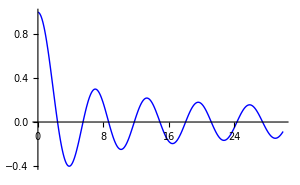
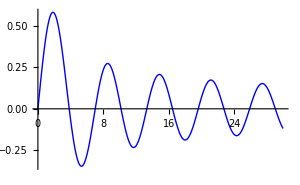
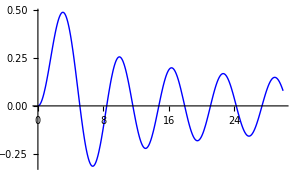
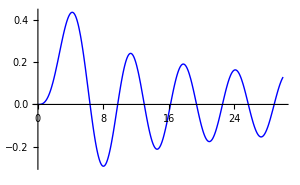
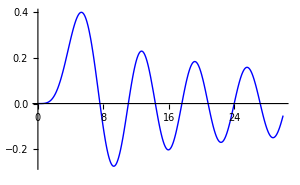
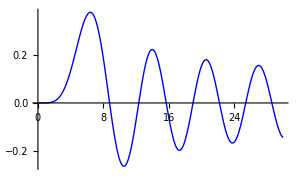
τάξη συνάρτησης Bessel 1ου είδους  |  γραφική παράσταση
0 | -Graphics-
1 | -Graphics-
2 | -Graphics-
3 | -Graphics-
4 | -Graphics-
5 | -Graphics-

```mathematica
ClearAll["Global`*"]
t1=Table[{n,Plot[BesselJ[n,x] ,{x,0,30},PlotStyle->{Blue,Thick},PlotLegends->"Expressions"  , PlotRange->All,  ImageSize->300]} ,{n,0,5}] ;
TableForm[t1,,TableSpacing->{1,10}, 
TableAlignments->Center,TableHeadings->{None,{" τ:03acξη συν:03acρτησης Bessel 1ου ε:03afδους "," γραφικ:03ae παρ:03acσταση"}}]
```

β)

```mathematica
ClearAll["Global`*"]  
data=Table[  N[BesselJZero [n,k] ],{k,1,5},{n,0,5}]  ;
TableForm[ data ,TableSpacing->{3,5}, 
TableAlignments->Center,TableHeadings->{{  1,2,3 ,4,5},{"0x","1x","2x","3x","4x","5x"}}]


f3 = D[BesselJ [3,x],x] ;
f4 = D[BesselJ [4,x],x] ;
f5 = D[BesselJ [5,x],x] ;
t3=Union[Table[x/.FindRoot[f3 ,{x,k} ,WorkingPrecision->10],{k,2,20,2}]];
t4=Table[x/.FindRoot[f4 ,{x,k} ,WorkingPrecision->10],{k,2,20,2}] //Union ;
t5=Table[x/.FindRoot[f5 ,{x,k} ,WorkingPrecision->10],{k,2,20,2}] //Union ;
s3={ 5.2725*10^-6,4.20118894,8.0152366,11.34592431,14.5858482};
s4= {0.0000189,5.317553,9.28239627,12.68190844,15.9641070};
s5= {0.00002439,6.4156163,10.5198609,13.9871886,17.3128424};
data={s3,s4,s5};
TableForm[ data,TableSpacing->{3,7}, TableDirections->Row,
TableAlignments->Center,TableHeadings->{{" J_3:0384(x)"," J_4:0384(x)"," J_5:0384(x)"},{ 1,2,3,4,5}}]
```

| 0x | 1x | 2x | 3x | 4x | 5x
1 | 2.40483 | 3.83171 | 5.13562 | 6.38016 | 7.58834 | 8.77148
2 | 5.52008 | 7.01559 | 8.41724 | 9.76102 | 11.0647 | 12.3386
3 | 8.65373 | 10.1735 | 11.6198 | 13.0152 | 14.3725 | 15.7002
4 | 11.7915 | 13.3237 | 14.796 | 16.2235 | 17.616 | 18.9801
5 | 14.9309 | 16.4706 | 17.9598 | 19.4094 | 20.8269 | 22.2178

|  J_3΄(x) |  J_4΄(x) |  J_5΄(x)
1 | 5.2725×10^-6 | 0.0000189 | 0.00002439
2 | 4.20119 | 5.31755 | 6.41562
3 | 8.01524 | 9.2824 | 10.5199
4 | 11.3459 | 12.6819 | 13.9872
5 | 14.5858 | 15.9641 | 17.3128

γ)

```mathematica
ClearAll["Global`*"]
eqbessel=x^2*y''[x]+x*y'[x]+(x^2 -n^2)y [x]==0
eb=DSolve[eqbessel,y[x],x]//TraditionalForm
```

(-n^2+x^2) y[x]+x y'[x]+x^2 y''[x]==0

{{y(x)→c_1 nx+c_2 nx}}

δ)

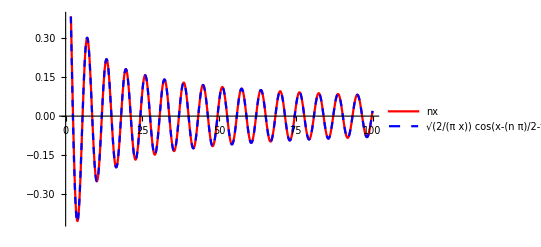
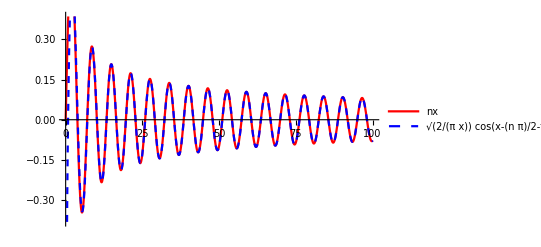
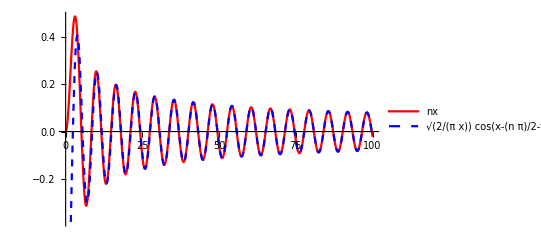
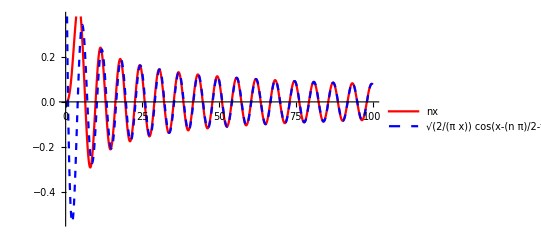
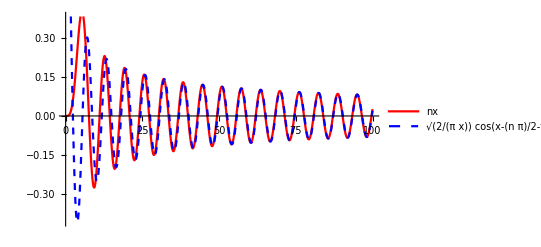
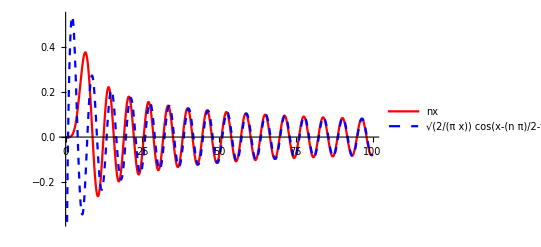
τάξη συνάρτησης Bessel 1ου είδους  |  γραφική παράσταση
0 | -Graphics-
1 | -Graphics-
2 | -Graphics-
3 | -Graphics-
4 | -Graphics-
5 | -Graphics-

```mathematica
ClearAll["Global`*"]
t=Table[{n,Plot[{BesselJ[n,x] ,√(2/(π*x))*Cos[x-(n*π)/2-π/4]},{x,0,100},PlotStyle->{{Red},{Blue,Dashed}},PlotLegends->"Expressions"  ,   ImageSize->400]} ,{n,0,5}]  ;
TableForm[t,TableSpacing->{3,10}, 
TableAlignments->Center,TableHeadings->{None,{" τ:03acξη συν:03acρτησης Bessel 1ου ε:03afδους "," γραφικ:03ae παρ:03acσταση"}}]
```

ε)

```mathematica
ClearAll["Global`*"]
a=1;
τ[k_] =BesselJZero[0,k];(* η k ρίζα της Subscript[J, 0](x) *) 
f[m_,n_]:= Integrate[ρ*BesselJ[0,τ[m]*ρ/a]*BesselJ[0,τ[n]*ρ/a],{ρ,0,a}]
g[x_]= a^2/2* D[BesselJ[0,x],x]^2;

(* α *)
f[1,1]==g[τ[1]]
f[1,2] 
(* β *)
f[10,10]==g[τ[10]]
f[20,50]
```

True

0

True

0

Ασκηση 3

α)

```mathematica
Clear["Global`*"]
c=2;
a=2;
b=3;
f[x_,y_]:=x*y*(2-x)(3-y)
g[x_,y_]:=0
μ[n_]=((n*π)/a)^2;
κ[m_]=((m*π)/b)^2;
λ[n_,m_]= μ[n]+ κ[m];
ω[n_,m_]=c*√λ[n,m] //Simplify;
Print["ω = ",ω[n,m]]
U[n_,m_]=Sin[(n*π*x)/a]*Sin[(m*π*y)/b];
A[n_,m_]=FullSimplify[4/(a *b)∫_0^b ∫_0^a f[x,y]*U[n,m]ⅆxⅆy,n∈Integers && m∈Integers ];
Print["TraditionalForm` = ",A[n,m]]
B[n_,m_]=4/(a *b*w[n,m])∫_0^b ∫_0^a g[x,y]*U[n,m]ⅆxⅆy;
Print["TraditionalForm` = ",B[n,m]]
T[n_,m_]=A[n,m]*Cos[ω[n,m]*t]+B[n,m]*Sin[ω[n,m]*t];

u[x_,y_,t_,l_,k_]:=∑_(n=1)^l ∑_(m=1)^k U[n,m]*T[n,m]

Print["\nΤο μερικό άθροισμα της σειράς αναπαράστασης της λύσης για n=m=5 είναι:"]
Solution[x_,y_,t_]=u[x,y,t,5,5] ;
Print[TraditionalForm[Solution[x,y,t]]]
```

ω = 1/3 √(4 m^2+9 n^2) π

TraditionalForm` = (576 (-1+(-1)^m) (-1+(-1)^n))/(m^3 n^3 π^6)

TraditionalForm` = 0

Το μερικό άθροισμα της σειράς αναπαράστασης της λύσης για n=m=5 είναι:

(2304 cos(1/3 √13 π t) sin((π x)/2) sin((π y)/3))/π^6+(256 cos(1/3 √85 π t) sin((3 π x)/2) sin((π y)/3))/(3 π^6)+(2304 cos(1/3 √229 π t) sin((5 π x)/2) sin((π y)/3))/(125 π^6)+(256 cos(√5 π t) sin((π x)/2) sin(π y))/(3 π^6)+(256 cos(√13 π t) sin((3 π x)/2) sin(π y))/(81 π^6)+(256 cos(√29 π t) sin((5 π x)/2) sin(π y))/(375 π^6)+(2304 cos(1/3 √109 π t) sin((π x)/2) sin((5 π y)/3))/(125 π^6)+(256 cos(1/3 √181 π t) sin((3 π x)/2) sin((5 π y)/3))/(375 π^6)+(2304 cos(5/3 √13 π t) sin((5 π x)/2) sin((5 π y)/3))/(15625 π^6)

β)

```mathematica
Animate[ParametricPlot3D[{x,y,Solution[x,y,t]},{x,0,2},{y,0,3}, PlotRange->{{0,2},{0,3},{-3,3}},BoundaryStyle->Directive[Blue,Thick],ColorFunction->"Rainbow",Mesh->True,BoxRatios->{1,1 ,1}],{t,0,4,0.002},AnimationRunning->False]
```

Ασκηση 4

α), β)

```mathematica
Clear["Global`*"]
a=1;
c=1;
x01=N[BesselJZero[0,1]];
f[r_]:=BesselJ[0,x01*r]
g[r_]:=0
x0[m_]:=N[BesselJZero[0,m]]
k[m_]:=x0[m]/a
ω[m_]:= c*k[m]
A[m_]:=(2∫_0^a r*BesselJ[0,k[m]*r] *f[r]ⅆr)/(a^2*BesselJ[1,x0[m]]^2)
B[m_]:=(2∫_0^a r*BesselJ[0,k[m]*r] *g[r]ⅆr)/(c*x0[m]*a*BesselJ[1,x0[m]]^2)



u[r_,t_,m_]:=(A[m]*Cos[ω[m]*t]+B[m]*Sin[ω[m]*t])*BesselJ[0,k[m]*r]
uapprox[r_,t_]=∑_(n=1)^5 u[r,t,n];

Animate[ParametricPlot3D[{r*Cos[θ],r*Sin[θ],uapprox[r,t]},{r,0,1},{θ,0,2Pi},PlotRange->{-1.2,1.2},BoundaryStyle->Directive[Red,Thick],ColorFunction->"SolarColors",Mesh->True],{t,0,6,0.01},AnimationRunning->False]
```

Ασκηση 5

Προσεγγιστική λύση

• Οι συντελεστές c = (a^-n (-2+n^2-4 Cos[n π]) Sin[n π])/(n (-4+n^2) π)   ,n≥0

• Οι συντελεστές d = (2 a^-n (-6+n^2-4 Cos[n π]) Sin[(n π)/2]^2)/(n (-4+n^2) π)   ,n≥1

Παρατηρούμε ότι c = 3/2 και c = -1/(4 a^2) ενώ για n≠0,2 τότε c = 0

Επίσης παρατηρούμε για n=2 όπου έχουμε απροσδιοριστία ότι d = 0

και d = 0                       για n άρτιο

Ενώ d = (a^(-1-2 k) (-2+8 k+8 k^2))/((1+2 k) (-3+4 k+4 k^2) π) για n περριτό

H προσεγγιστική λύση για α=3 για τους 20 πρώτους όρους είναι:
u(ρ,θ) = 3/4-1/36 ρ^2 Cos[2 θ]+(2 ρ Sin[θ])/(9 π)+(14 ρ^3 Sin[3 θ])/(405 π)+(46 ρ^5 Sin[5 θ])/(25515 π)+(94 ρ^7 Sin[7 θ])/(688905 π)+(158 ρ^9 Sin[9 θ])/(13640319 π)+(238 ρ^11 Sin[11 θ])/(227988189 π)+(334 ρ^13 Sin[13 θ])/(3419822835 π)+(446 ρ^15 Sin[15 θ])/(47566626705 π)+(574 ρ^17 Sin[17 θ])/(625684089735 π)+(718 ρ^19 Sin[19 θ])/(7883619530661 π)

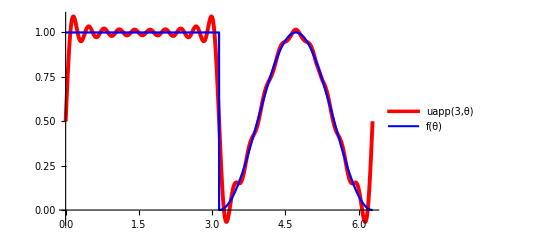

-Graphics3D-

```mathematica
ClearAll["Global`*"]

f[θ_]:=Which[0≤ θ≤ π,1,π<θ<2π,(Sin[θ])^2]

c[n_,a_]:=1/(π a^n)Integrate[f[θ]*Cos[n*θ],{θ,0,2π}] 
d[n_,a_]:=1/(π a^n)Integrate[f[θ]*Sin[n*θ],{θ,0,2π}] 

Print["• Οι συντελεστές c = ",Simplify[c[n,a]],"   ,n≥0"]
Print["• Οι συντελεστές d = ",Simplify[d[n,a]] ,"   ,n≥1"]
Print["\nΠαρατηρούμε ότι c = ",c[0,a]," και c = ",c[2,a]," ενώ για n≠0,2 τότε c = 0"]
Print["\nΕπίσης παρατηρούμε για n=2 όπου έχουμε απροσδιοριστία ότι d = ",d[2,a]]
Print["και d = ",Simplify[d[n,a]/.{n-> 2k} ,k ∈Integers] ,"                       για n άρτιο "]
Print["Ενώ d = ",Simplify[d[n,a]/.{n-> 2k+1} ,k ∈Integers] ," για n περριτό\n"]



U[ρ_,θ_,m_,a_]:=c[0,a]/2+Sum[ρ^n*c[n,a]*Cos[n*θ],{n,1,m}]+Sum[ρ^n*d[n,a]*Sin[n*θ],{n,1,m,1}] 


uapp[ρ_,θ_]=U[ρ,θ,20,3];
Print["\nH προσεγγιστική λύση για α=3 για τους 20 πρώτους όρους είναι:\nu(ρ,θ) = ",uapp[ρ,θ]]

Plot[ {uapp[3,θ ] ,f[θ]  },{θ,0,2π},PlotLegends->"Expressions",PlotStyle->{{Red,Thickness[0.007]},{Blue,Thickness[0.004]} }]

ParametricPlot3D[{ρ Cos[θ],ρ Sin[θ],uapp[ρ,θ]},{ρ,0,3},{θ,0,2π},PlotRange->All,BoundaryStyle->Red,ViewPoint->{-2,-1,1},ImageSize->Large]
```

Ακριβή λύση

Για α=3

Οι συντελεστές d = (3^(-1-2 k) (-2+8 k (1+k)))/((1+2 k) (-3+4 k (1+k)) π)   ,n≥1 και n περριτός

Η ακριβή λύση:

3/4-1/36 ρ^2 Cos[2 θ]-1/(405 π)ⅈ ⅇ^(-3 ⅈ θ) ρ (-45 ⅇ^(2 ⅈ θ) Hypergeometric2F1[-1/2,1,5/2,1/9 ⅇ^(-2 ⅈ θ) ρ^2]+45 ⅇ^(4 ⅈ θ) Hypergeometric2F1[-1/2,1,5/2,1/9 ⅇ^(2 ⅈ θ) ρ^2]-4 ρ^2 Hypergeometric2F1[1/2,2,7/2,1/9 ⅇ^(-2 ⅈ θ) ρ^2]+4 ⅇ^(6 ⅈ θ) ρ^2 Hypergeometric2F1[1/2,2,7/2,1/9 ⅇ^(2 ⅈ θ) ρ^2]-4 ρ^2 HypergeometricPFQ[{1/2,2,2},{1,7/2},1/9 ⅇ^(-2 ⅈ θ) ρ^2]+4 ⅇ^(6 ⅈ θ) ρ^2 HypergeometricPFQ[{1/2,2,2},{1,7/2},1/9 ⅇ^(2 ⅈ θ) ρ^2])

Απ'ότι φαίνεται η απειροσειρά δεν μπορεί να υπολογιστεί σε κλειστή μορφή και το mathematica χρησιμοποιεί υπεργεωμετρική κατανομή.
Οπότε η λύση που παρουσιάζεται στα γραφήματα δεν είναι η ακριβή λύση αλλά είναι σαν να έχουμε βάλει έναν αρκετά μεγάλο αριθμό για n στο παραπάνω άθροισμα.

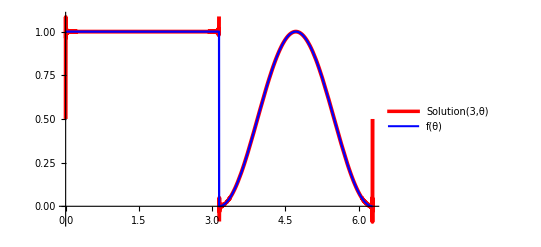

-Graphics3D-

```mathematica
(*Σύμφωνα με τους παραπάνω υπολογισμούς, απλοποιώντας τους συντελεστές Subscript[d, n] έχουμε: *)
Print["Για α=3"]
Print["Οι συντελεστές d = ",FullSimplify[d[n,3]/.{n-> 2k+1} ,k ∈Integers],"   ,n≥1 και n περριτός"]


Print["Η ακριβή λύση:"]
Solution[ρ_,θ_]=3/4-1/36 ρ^2 Cos[2 θ]+Sum[(ρ/3)^(1+2 k)*(-2+8 k (1+k))/((1+2 k) (-3+4 k (1+k)) π)*Sin[(1+2 k)*θ],{k,0,∞}]
Print["Απ'ότι φαίνεται η απειροσειρά δεν μπορεί να υπολογιστεί σε κλειστή μορφή και το mathematica χρησιμοποιεί υπεργεωμετρική κατανομή.\nΟπότε η λύση που παρουσιάζεται στα γραφήματα δεν είναι η ακριβή λύση αλλά είναι σαν να έχουμε βάλει έναν αρκετά μεγάλο αριθμό για n στο παραπάνω άθροισμα."]


Plot[ {Solution[3,θ ] ,f[θ]  },{θ,0,2π},PlotLegends->"Expressions",PlotStyle->{{Red,Thickness[0.007]},{Blue,Thickness[0.004]},{Green,Dashed,Thickness[0.005]} }]

ParametricPlot3D[{ρ Cos[θ],ρ Sin[θ],Solution[ρ,θ]},{ρ,0,3},{θ,0,2π},PlotRange->All,BoundaryStyle->Red,ViewPoint->{-2,-1,1},ImageSize->Large]
```

Ασκηση 6

```mathematica
ClearAll["Global`*"]
psum[r_,θ_,m_]:=Sum[c[n] r^n  LegendreP[n, Cos[θ]],{n,0,m}] 
c[n_]:= (2n+1)/(2 a^n)* Integrate[f[θ]*LegendreP[n,Cos[θ] ]*Sin[θ ],{θ,0,π}]  
a=1 ;
f[θ_]=(Cos[θ])^2+2;  

Solution[r_,θ_]=psum[r,θ,10]//TraditionalForm;
Print["Η λύση u(r,θ) = ",Solution[r,θ]]

TableForm[Table[N[Solution[r,θ] ],{r,1/4,3/4,1/4},{θ,0,π,π/4}],TableHeadings->{{"u(1/4,θ)","u(1/2,θ)","u(3/4,θ)"},{"0","π/4","π/2","(3  π)/4","π"}},TableAlignments->Center]
```

Η λύση u(r,θ) = 1/3 r^2 (3 cos^2(θ)-1)+7/3

| 0 | π/4 | π/2 | (3  π)/4 | π
u(1/4,θ) | 2.375 | 2.34375 | 2.3125 | 2.34375 | 2.375
u(1/2,θ) | 2.5 | 2.375 | 2.25 | 2.375 | 2.5
u(3/4,θ) | 2.70833 | 2.42708 | 2.14583 | 2.42708 | 2.70833